```mathematica
irrationalQ[x_]:=!Element[x,Rationals]
```

```mathematica
FindEquationalProof[ForAll[{x,y},irrationalQ[x]&&irrationalQ[y],Not[Element[x+y,Rationals]]],Method->{"QuantifierElimination","DisjunctiveForm"->True}]
```

Part::partw: Part 1 of {} does not exist.

FindEquationalProof::invs: Invalid specification of propositions ∀_({x,y},x∉&&y∉)x+y∉ and axioms Method→{QuantifierElimination,DisjunctiveForm→True}.

FindEquationalProof[∀_({x,y},x∉ℚ&&y∉ℚ)x+y∉ℚ,Method→{QuantifierElimination,DisjunctiveForm→True}]

```mathematica
ForAll[{x,y},irrationalQ[x]&&irrationalQ[y],Not[Element[x+y,Rationals]]]
(Element[x+y,Rationals]&&irrationalQ[x]&&irrationalQ[y])||(Element[x+y,Reals]&&Not[Element[x+y,Rationals]]&&irrationalQ[x]&&irrationalQ[y])
```

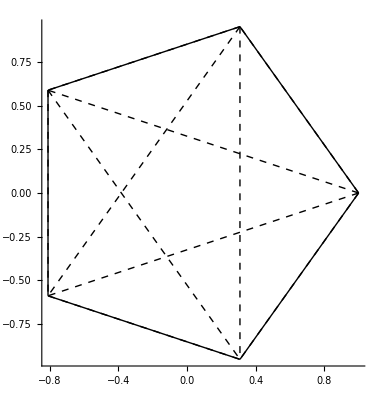

```mathematica
ClearAll[drawPolygonWithChords];
drawPolygonWithChords[n_Integer/;n>=3]:=Module[{points,lines,polygon,chords},points=Table[{Cos[2 Pi k/n],Sin[2 Pi k/n]},{k,0,n-1}];
lines=Line/@Partition[points,2,1,1];
polygon=Graphics[lines];
chords=Graphics[{Dashed,Line/@Subsets[points,{2}]}];
Show[polygon,chords,PlotRange->1.2,Axes->True]]

drawPolygonWithChords[5] (*for example,with n=5*)
```

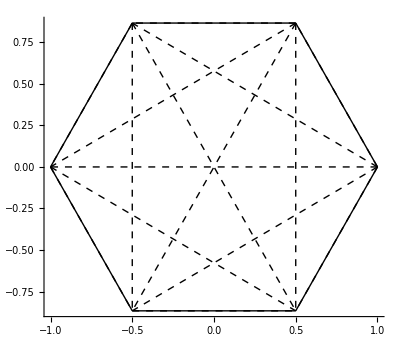

```mathematica
drawPolygonWithChords[6]
```

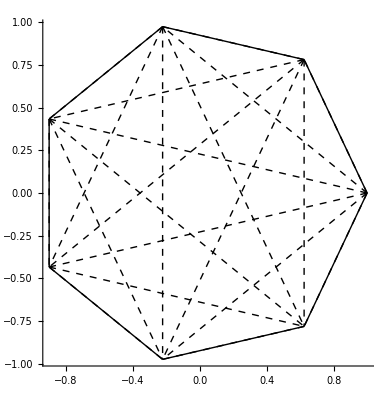

```mathematica
drawPolygonWithChords[7]
```

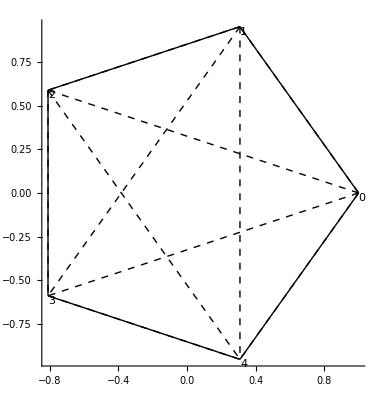
{-Graphics-,{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}}

```mathematica
ClearAll[drawPolygonWithChords];
drawPolygonWithChords[n_Integer/;n>=3]:=Module[{points,lines,polygon,chords,labels,chordList},points=Table[{Cos[2 Pi k/n],Sin[2 Pi k/n]},{k,0,n-1}];
lines=Line/@Partition[points,2,1,1];
polygon=Graphics[lines];
chords=Graphics[{Dashed,Line/@Subsets[points,{2}]}];
labels=Table[Text[k,points[[k+1]],{-1,1}],{k,0,n-1}];
labeledPolygon=Show[polygon,chords,Graphics[labels],PlotRange->1.2,Axes->True];
chordList=Subsets[Range[n],{2}];
{labeledPolygon,chordList}]

result=drawPolygonWithChords[5] (*for example,with n=5*)
```

```mathematica
omitAdjacentPairs[pairs_]:=Module[
{length,list },
list={};
length=Length@pairs;
For[i=1,i<length,i++,
If[Abs[pairs[[i,1]]-pairs[[i,2]]]!=1,
AppendTo[list,pairs[[i]]];
]
];
list]
```

```mathematica
1==1
```

True

```mathematica
Length@result[[2]]
noAdjacentPairs=omitAdjacentPairs[result[[2]]]
```

10

{{1,3},{1,4},{1,5},{2,4},{2,5},{3,5}}

```mathematica
result[[2,1]]
```

{1,2}

```mathematica
intersectingChordsOfNGon[n_]:=Module[
{length,list ,list2,vertexPairs},
(*Generate pairs of numbers from [n]*)
vertexPairs=Subsets[Table[i,{i,1,n}],{2}];
list={};
length=Length@vertexPairs;
For[i=1,i<length,i++,
(*Generate list of non-adjacent vertex pairs*)
If[Abs[vertexPairs[[i,1]]-vertexPairs[[i,2]]]!=1,
AppendTo[list,vertexPairs[[i]]];
]
];
(*For each resulting pair, count the pairs which crosses it*)
For[i=1, i<Length@list,i++,

]
list

]
```

```mathematica
Permu
```

```mathematica
ClearAll[generatePairs];
generatePairs[numbers_List]:=Subsets[numbers,{2}]

inputList={1,2,3,4};
pairs=generatePairs[inputList]
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

```mathematica
Subsets[Table[i,{i,1,4}],{2}]
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

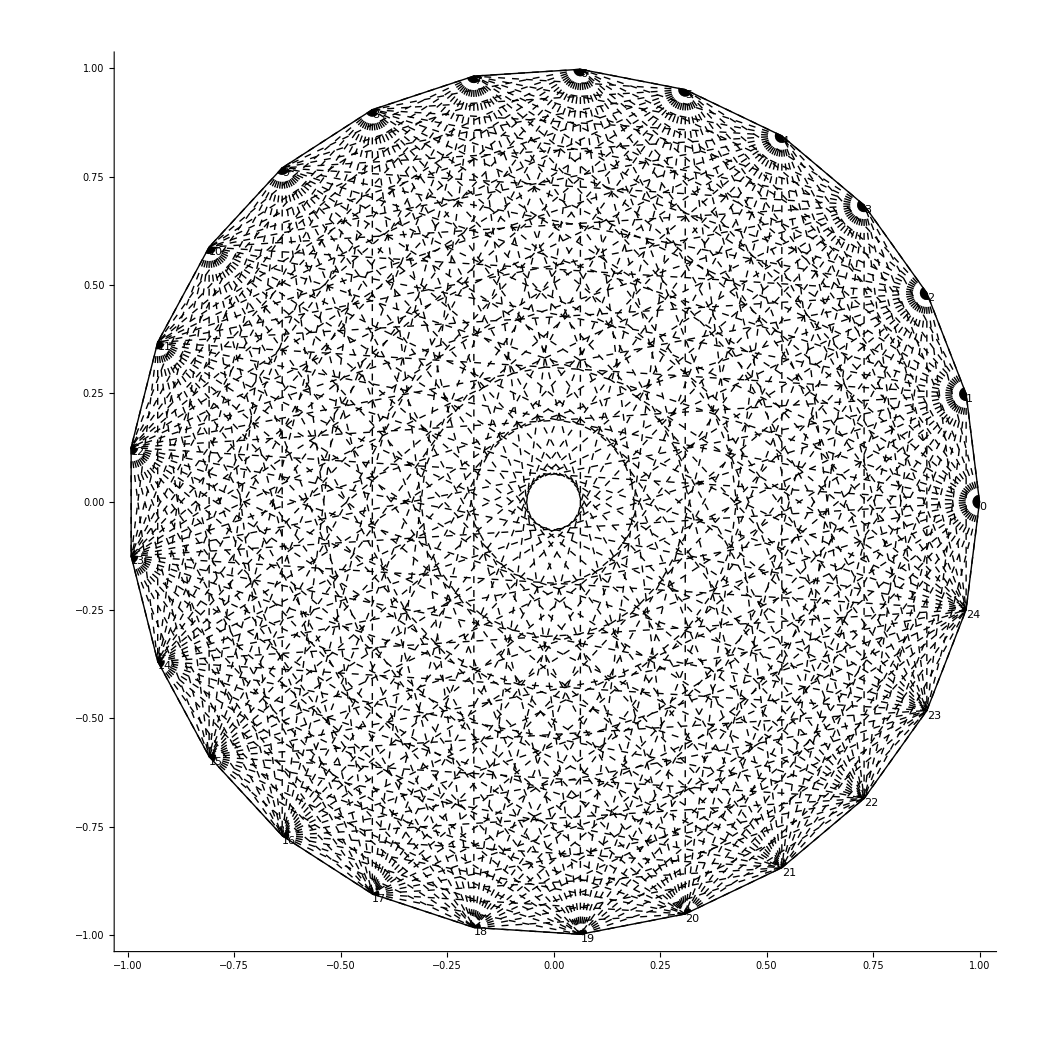
{-Graphics-,{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{2,21},{2,22},{2,23},{2,24},{2,25},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{3,21},{3,22},{3,23},{3,24},{3,25},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{4,21},{4,22},{4,23},{4,24},{4,25},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20},{5,21},{5,22},{5,23},{5,24},{5,25},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{6,20},{6,21},{6,22},{6,23},{6,24},{6,25},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{7,20},{7,21},{7,22},{7,23},{7,24},{7,25},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{8,20},{8,21},{8,22},{8,23},{8,24},{8,25},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{9,25},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21},{10,22},{10,23},{10,24},{10,25},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{11,21},{11,22},{11,23},{11,24},{11,25},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21},{12,22},{12,23},{12,24},{12,25},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{13,21},{13,22},{13,23},{13,24},{13,25},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{14,21},{14,22},{14,23},{14,24},{14,25},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21},{15,22},{15,23},{15,24},{15,25},{16,17},{16,18},{16,19},{16,20},{16,21},{16,22},{16,23},{16,24},{16,25},{17,18},{17,19},{17,20},{17,21},{17,22},{17,23},{17,24},{17,25},{18,19},{18,20},{18,21},{18,22},{18,23},{18,24},{18,25},{19,20},{19,21},{19,22},{19,23},{19,24},{19,25},{20,21},{20,22},{20,23},{20,24},{20,25},{21,22},{21,23},{21,24},{21,25},{22,23},{22,24},{22,25},{23,24},{23,25},{24,25}}}

```mathematica
drawPolygonWithChords[25]
```